```mathematica
FullSimplify[d2nde==((1/σe^2+ ϕN) ϕR)/(  ρ^2 χ^2(1-(ν ρ σc σe γ^-1)^2)-ϕN ϕR)&&d2rde==(ϕN ϕR+ρ^2 χ^2((1-ϕR/χ)^2+  σe^2 ϕN ))/(ρ^2 χ^2(1-(ν ρ σc σe γ^-1)^2)-ϕN ϕR)/.Solve[d2nde==ϕR/(σe ρ χ)^2(d2rde+1)&&d2rde==σe^2 ϕN(d2nde+1)+(ρ σe σc γ^-1 ν)^2(d2rde+1),{d2nde,d2rde}]/.First@Solve[ν ρ σc σe γ^-1==1-ϕR/χ,ν],γ>0]
```

{True}

```mathematica
Sin[π/2-θ]
```

Cos[θ]

```mathematica
First@Solve[ν ρ σc σe γ^-1==1-ϕR/χ,ν]
```

{ν→-(γ (ϕR-χ))/(ρ σc σe χ)}

```mathematica
{{ϕR->((γ-ν ρ σc σe) χ)/γ}}
```

```mathematica
Solve[d2nde==ϕR/(σe ρ χ)^2(d2rde+1)&&d2rde==σe^2 ϕN(d2nde+1)+(ρ σe σc γ^-1 ν)^2(d2rde+1),{d2nde,d2rde}]
```

{{d2nde→-(γ^2 (1+σe^2 ϕN) ϕR)/(σe^2 (γ^2 ϕN ϕR-γ^2 ρ^2 χ^2+ν^2 ρ^4 σc^2 σe^2 χ^2)),d2rde→-(-γ^2 ϕN ϕR-ν^2 ρ^4 σc^2 σe^2 χ^2-γ^2 ρ^2 σe^2 ϕN χ^2)/(-γ^2 ϕN ϕR+γ^2 ρ^2 χ^2-ν^2 ρ^4 σc^2 σe^2 χ^2)}}

```mathematica
Solve[d2nde==ϕN/(σe ρ χ)^2(d2rde+1)&&d2rde==σe^2 ϕR(d2nde+1)+(ρ σe σc γ^-1 ν)^2(d2rde+1),{d2nde,d2rde}]
```

{{d2nde→-(γ^2 ϕN (1+σe^2 ϕR))/(σe^2 (γ^2 ϕN ϕR-γ^2 ρ^2 χ^2+ν^2 ρ^4 σc^2 σe^2 χ^2)),d2rde→-(-γ^2 ϕN ϕR-ν^2 ρ^4 σc^2 σe^2 χ^2-γ^2 ρ^2 σe^2 ϕR χ^2)/(-γ^2 ϕN ϕR+γ^2 ρ^2 χ^2-ν^2 ρ^4 σc^2 σe^2 χ^2)}}

```mathematica
FullSimplify[γ^2 σe ϕN ϕR+ρ^2 σe (-γ+ν ρ σc σe) (γ+ν ρ σc σe) χ^2==0/.First@Solve[ν ρ σc σe γ^-1==1-ϕR/χ,ν]]
```

γ σe ϕR (ϕN+ρ^2 (ϕR-2 χ))==0

```mathematica
Solve[d2nde+1==ϕR/(σe ρ χ)^2(d2rde+1)&&d2rde+1==σe^2 ϕN(d2nde+1)+(ρ σe σc γ^-1 ν)^2(d2rde+1),{d2nde,d2rde}]
```

{{d2nde→-1,d2rde→-1}}

```mathematica
Solve[d2nde+1==ϕR/(σe ρ χ)^2(d2rde+1)&&d2rde==σe^2 ϕN(d2nde+1)+(ρ σe σc γ^-1 ν)^2(d2rde+1),{d2nde,d2rde}]
```

```mathematica
ListPlot[]
```

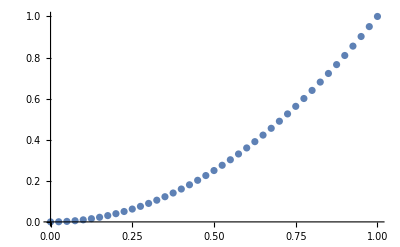

```mathematica
ListPlot[Transpose[{Range[0,1,0.025],Range[0,1,0.025]^2}]]
```

```mathematica
Length[Range[0,1,0.025]]/Length[Range[0,1,0.02]]//N
```

0.803922

```mathematica
Solve[(σc σe χ)^2(dnde2)+ϕR σc^2(drde2+1)==0&&ϕN σe^2(dnde2+1)+(ρ σe σc γ^-1 ν-1)^2(drde2+1)==0,{dnde2,drde2}]
```

{{dnde2→-(γ^2 ϕN ϕR)/(γ^2 ϕN ϕR-γ^2 χ^2+2 γ ν ρ σc σe χ^2-ν^2 ρ^2 σc^2 σe^2 χ^2),drde2→-(γ^2 ϕN ϕR-γ^2 χ^2+2 γ ν ρ σc σe χ^2-ν^2 ρ^2 σc^2 σe^2 χ^2-γ^2 σe^2 ϕN χ^2)/(γ^2 ϕN ϕR-γ^2 χ^2+2 γ ν ρ σc σe χ^2-ν^2 ρ^2 σc^2 σe^2 χ^2)}}

```mathematica
ClearAll@ρ
```

```mathematica
FullSimplify[Solve[(ρ σc σe χ)^2(dnde2+1)+ϕR σc^2(drde2)==0&&ϕN σe^2(dnde2)+(ρ σe σc γ^-1 ν-1)^2(drde2+1)==0,{dnde2,drde2}](*/.ν->-ϕN/(σc σe ρ χ)*),γ>0]
```

```mathematica
FullSimplify[dnde2==((γ-ν ρ σc σe)^2 (ϕR-ρ^2 σe^2 χ^2)/(σe^2 γ^2))/(- ϕN ϕR+ρ^2 (1-ν ρ σc σe/γ)^2 χ^2)/.Solve[(ρ σc σe χ)^2(dnde2+1)+ϕR σc^2(drde2)==0&&ϕN σe^2(dnde2)+(ρ σe σc γ^-1 ν-1)^2(drde2+1)==0,{dnde2,drde2}](*/.ν->-ϕN/(σc σe ρ χ)*),γ>0]
```

{True}

```mathematica
Solve[(σc σe χ)^2(dnde2)+ϕR σc^2(drde2+1)==0&&ϕN σe^2(dnde2+1)+(ρ σe σc γ^-1 ν-1)^2(drde2)==0,{dnde2,drde2}]
```

{{dnde2→-(-σc^2 (-1+(ν ρ σc σe)/γ)^2 ϕR+σc^2 σe^2 ϕN ϕR)/(σc^2 σe^2 ϕN ϕR-σc^2 σe^2 (-1+(ν ρ σc σe)/γ)^2 χ^2),drde2→-(-γ^2 ϕN ϕR+γ^2 σe^2 ϕN χ^2)/(-γ^2 ϕN ϕR+γ^2 χ^2-2 γ ν ρ σc σe χ^2+ν^2 ρ^2 σc^2 σe^2 χ^2)}}

```mathematica
FullSimplify[1-σα^2 ((-χ (-1+γ σα^2 χ))+γ χ (2-γ σα^2 χ))]
```

(-1+γ σα^2 χ) (-1+(1+γ) σα^2 χ)

```mathematica
FullSimplify[X==1+(2 σα^2 ϕ)/(1-σα^2 (ϕ+γ χ (2-γ σα^2 χ)))/.First@Solve[X==(ϕ σα^2)/((σα^2 γ χ-1)^2)(X+1)+1,X]]
```

True

```mathematica
1+σα^2 (-ϕ+γ χ (-2+γ σα^2 χ))
```

```mathematica
1/σα/.Solve[FullSimplify[1+σα^2 (-ϕ+γ χ (-2+γ σα^2 χ))/.First@Solve[χ==ϕ/(1-χ γ σα^2),χ]]==0,σα]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{-√(ϕ+2 γ ϕ+γ^2 ϕ),√(ϕ+2 γ ϕ+γ^2 ϕ)}

```mathematica
FullSimplify[dnde2==((1/σe^2+ ϕN γ^-1) ϕR)/(ρ^2 χ^2(1-(ϕN χ^-1 γ^-1)^2)-ϕN ϕR γ^-1)&&drde2==(γ^-1 ϕN ϕR+ ρ^2 χ^2((ϕN χ^-1 γ^-1)^2+γ^-1 ϕN σe^2 ))/(ρ^2 χ^2(1-(ϕN χ^-1 γ^-1)^2)-γ^-1 ϕN ϕR)/.First@Solve[dnde2==ϕR/(σe^2 ρ^2 χ^2)(drde2+1)&&drde2==γ^-1 ϕN σe^2(dnde2+1)+(ρ σe σc γ^-1 ν)^2(drde2+1),{dnde2,drde2}]/.First@Solve[ν==-ϕN/(σc σe ρ χ),χ]]
```

True

```mathematica
Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]
```

{{χ→(-ϕN+γ ϕR)/γ,ν→(γ ϕN)/(ρ σc σe (ϕN-γ ϕR))}}

```mathematica
Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]
```

{{χ→(-ϕN+γ ϕR)/γ,ν→(γ ϕN)/(ρ σc σe (ϕN-γ ϕR))}}

```mathematica
FullSimplify[(-ϕN+γ ϕR)/γ==-ϕN/γ+ ϕR]
```

True

```mathematica
FullSimplify[(√ϕN)/(√(-2 ϕN+γ ϕR))==(γ ϕR/ϕN-2)^(-1/2),ϕN>0]
```

True

```mathematica
Tan
```

```mathematica
Solve[ρ^2 ϕR-(1+2 ρ^2)γ^-1 ϕN==0,ρ]
```

{{ρ→-(√ϕN)/(√(-2 ϕN+γ ϕR))},{ρ→(√ϕN)/(√(-2 ϕN+γ ϕR))}}

```mathematica
FullSimplify[ρ^2 χ^2(1-(ϕN χ^-1 γ^-1)^2)-γ^-1 ϕN ϕR/.Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]]
```

{(ϕR (-((1+2 ρ^2) ϕN)+γ ρ^2 ϕR))/γ}

```mathematica
ρ^2 χ^2(1-(ϕN χ^-1 γ^-1)^2)-γ^-1 ϕN ϕR
```

-(ϕN ϕR)/γ+ρ^2 (1-ϕN^2/(γ^2 χ^2)) χ^2

```mathematica
FullSimplify[χ^2/.First@Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]]
```

(ϕN-γ ϕR)^2/γ^2

```mathematica
FullSimplify[(1-(ϕN χ^-1 γ^-1)^2)/.First@Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]]
```

1-ϕN^2/(ϕN-γ ϕR)^2

```mathematica
FullSimplify[(ϕN-γ ϕR)^2/γ^2(1-ϕN^2/(ϕN-γ ϕR)^2)]
```

ϕR (-(2 ϕN)/γ+ϕR)

```mathematica
FullSimplify[(ϕR (-((1+2 ρ^2) ϕN)+γ ρ^2 ϕR))/γ==ϕR ( ρ^2 ϕR-(1+2 ρ^2) γ^-1 ϕN)]
```

True

```mathematica
ρ σe σc ν/.Solve[ν==-ϕN/(σc σe ρ χ),ν]
```

{-ϕN/χ}

```mathematica
Solve[dnde2==ϕR/(σe^2 ρ^2 χ^2)(drde2+1)&&drde2==γ^-1 ϕN σe^2(dnde2+1)+(ρ σe σc γ^-1 ν)^2(drde2+1),{dnde2,drde2}]
```

{{dnde2→-(γ (γ+σe^2 ϕN) ϕR)/(σe^2 (γ ϕN ϕR-γ^2 ρ^2 χ^2+ν^2 ρ^4 σc^2 σe^2 χ^2)),drde2→-(-γ ϕN ϕR-ν^2 ρ^4 σc^2 σe^2 χ^2-γ ρ^2 σe^2 ϕN χ^2)/(-γ ϕN ϕR+γ^2 ρ^2 χ^2-ν^2 ρ^4 σc^2 σe^2 χ^2)}}

```mathematica
Solve[χ==ϕ/(1-χ γ σα^2),γ]
```

```mathematica
(1-γ σα^2 χ) (1-(1+γ) σα^2 χ)/.First@Solve[χ==ϕ/(1-χ γ σα^2),γ]
```

(1-(-ϕ+χ)/χ) (1-σα^2 χ (1+(-ϕ+χ)/(σα^2 χ^2)))

```mathematica
FullSimplify[(1+σα^2 ϕN-2 γ σα^2 χ+γ^2 σα^4 χ^2)/(1-σα^2 ϕN-2 γ σα^2 χ+γ^2 σα^4 χ^2)]
```

1+(2 σα^2 ϕN)/(1+σα^2 (-ϕN+γ χ (-2+γ σα^2 χ)))

{∞,{γ→Indeterminate,σα→Indeterminate,ϕN→Indeterminate,χ→Indeterminate}}

```mathematica
Solve[χ==ϕ/(1-χ γ σα^2),ϕ]
```

{{ϕ→-χ (-1+γ σα^2 χ)}}

```mathematica
Solve[D[V0((σ/x)^12+(σ/x)^6),x]==0,x]
```

{{x→-(-2)^(1/6) σ},{x→(-2)^(1/6) σ},{x→-(-2)^(1/6) (-1)^(1/3) σ},{x→(-2)^(1/6) (-1)^(1/3) σ},{x→-(-2)^(1/6) (-1)^(2/3) σ},{x→(-2)^(1/6) (-1)^(2/3) σ}}

```mathematica
Solve[D[V0((σ/x)^12+(σ/x)^6),x]==0,x]
```

```mathematica
D[V0((σ/x)^12+(σ/x)^6),{x,3}]
```

V0 (-(336 σ^6)/x^9-(2184 σ^12)/x^15)

```mathematica
FullSimplify[(1-β)/(1+β)==1-(2β)/(1+β)]
```

True

```mathematica
Series[√((1-β)/(1+β)),{β,0,1}]
```

1-β+O[β]^2

```mathematica
FullSimplify[1-1/2(2β)/(1+β)]
```

1/(1+β)

```mathematica
First@Solve[XN+1==ϕR/(σe ρ χ)^2(XR+1)&&XR+1==(σe^2 γ^-1 ϕN)/((1-ρ σe σc γ^-1 ν)^2)(XN+1),{XN,XR}]
```

{XN→-1,XR→-1}

```mathematica
FullSimplify[XN==(ϕR((1-ν ρ σc σe γ^-1)^2 σe^-2+γ^-1  ϕN))/(ρ^2 χ^2(1-ν ρ σc σe γ^-1)^2-γ^-1 ϕN ϕR)&&XR==(γ^-1 ϕN( ϕR+ρ^2 σe^2  χ^2))/(ρ^2 χ^2(1-γ^-1 ν ρ σc σe)^2-γ^-1 ϕN ϕR)/.First@Solve[XN==ϕR/(σe ρ χ)^2(XR+1)&&XR==(σe^2 γ^-1 ϕN)/((1-ρ σe σc γ^-1 ν)^2)(XN+1),{XN,XR}]]
```

True

```mathematica
FullSimplify[ρ^2 χ^2(1-γ^-1 ν ρ σc σe)^2-γ^-1 ϕN ϕR==(ρ^2 χ^2(1-γ^-1 ν ρ σc σe)^2-γ^-1 ϕN ϕR)]
```

```mathematica
FullSimplify[χ== ϕR-γ^-1 ϕN/.First@Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]]
```

True

```mathematica
FullSimplify[XN==(ϕR(((γ ϕR)/(-ϕN+γ ϕR))^2 σe^-2+γ^-1  ϕN))/(ρ^2 χ^2((γ ϕR)/(-ϕN+γ ϕR))^2-γ^-1 ϕN ϕR)/.{XN->(ϕR((1-ν ρ σc σe γ^-1)^2 σe^-2+γ^-1  ϕN))/(ρ^2 χ^2(1-ν ρ σc σe γ^-1)^2-γ^-1 ϕN ϕR),XR->(γ^-1 ϕN( ϕR+ρ^2 σe^2  χ^2))/(ρ^2 χ^2(1-γ^-1 ν ρ σc σe)^2-γ^-1 ϕN ϕR)}/.First@Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]]
```

True

```mathematica
FullSimplify[ϕN/ϕR/.First@Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{ϕN,ϕR}]]
```

γ+γ^2/(-γ+ν ρ σc σe)

```mathematica
FullSimplify[1+ϕN (ϕR-γ^-1 ϕN)^-1  γ^-1]
```

(γ ϕR)/(-ϕN+γ ϕR)

```mathematica
FullSimplify[χ== ϕR-γ^-1 ϕN/.First@Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]]
```

True

```mathematica
FullSimplify[(ρ^2 χ^2(1-γ^-1 ν ρ σc σe)^2-γ^-1 ϕN ϕR)/.First@Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]]
```

```mathematica
Solve[ϕR (-ϕN/γ+ρ^2 ϕR)==0,ρ]
```

{{ρ→-(√ϕN)/(√γ √ϕR)},{ρ→(√ϕN)/(√γ √ϕR)}}

```mathematica
FullSimplify[ρ σc σe ν== (γ^-1- ϕR/ϕN)^-1&&χ==ϕR-γ^-1 ϕN/.First@Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]]
```

True

```mathematica
FullSimplify[ρ^2 χ^2(1-γ^-1 ν ρ σc σe)^2-γ^-1 ϕN ϕR/.First@Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]]
```

ϕR (-ϕN/γ+ρ^2 ϕR)

```mathematica
1-2X+X^2
```

1-2 X+X^2

```mathematica
Simplify[1-2 X+X^2]
```

(-1+X)^2

```mathematica
First@Solve[XN==ϕR/(σe ρ χ)^2(XR+1)&&XR==(σe^2 γ^-1 ϕN)/((1-ρ σe σc γ^-1 ν)^2)(XN+1),{XN,XR}]
```

{XN→-(ϕR/(ρ^2 σe^2 χ^2)+(ϕN ϕR)/(γ ρ^2 (1-(ν ρ σc σe)/γ)^2 χ^2))/(-1+(ϕN ϕR)/(γ ρ^2 (1-(ν ρ σc σe)/γ)^2 χ^2)),XR→-(-γ ϕN ϕR-γ ρ^2 σe^2 ϕN χ^2)/(-γ ϕN ϕR+γ^2 ρ^2 χ^2-2 γ ν ρ^3 σc σe χ^2+ν^2 ρ^4 σc^2 σe^2 χ^2)}

```mathematica
FullSimplify[drde2==(γ^-1(1+ ρ^2 σe^2 χ^2))/(-γ^-1+χ^2 ρ^2 (1-γ^-1 ν ρ σc σe)^2)&&dnde2==(ν^2 ρ^2 σc^2 γ^-2+1/σe^2+-2 ν ρ σc σe^-1 γ^-1+γ^-1)/(-γ^-1+(χ ρ (1-γ^-1 ν ρ σc σe))^2)/.First@Solve[dnde2==1/(σe ρ χ)^2(drde2+1)&&drde2==(σe^2 γ^-1)/((1-ρ σe σc γ^-1 ν)^2)(dnde2+1),{dnde2,drde2}]]
```

True

```mathematica
FullSimplify[First@Solve[dnde2==1/(σe ρ χ)^2(drde2+1)&&drde2==(σe^2 γ^-1)/((1-ρ σe σc γ^-1 ν)^2)(dnde2+1),{dnde2,drde2}]]
```

{dnde2→(γ^2+ν^2 ρ^2 σc^2 σe^2+γ σe (-2 ν ρ σc+σe))/(σe^2 (-γ+ρ^2 (γ-ν ρ σc σe)^2 χ^2)),drde2→(γ+γ ρ^2 σe^2 χ^2)/(-γ+ρ^2 (γ-ν ρ σc σe)^2 χ^2)}

```mathematica
FullSimplify[(γ^2+ν^2 ρ^2 σc^2 σe^2+γ σe (-2 ν ρ σc+σe))/(σe^2 (-γ+ρ^2 (γ-ν ρ σc σe)^2 χ^2))==((ν^2 ρ^2 σc^2)/γ^2+1/σe^2+(-2 ν ρ σc+σe)/(γ σe))/(-γ^-1+χ^2 ρ^2 (1-γ^-1 ν ρ σc σe)^2 )]
```

True

```mathematica
FullSimplify[-γ^-1+(χ ρ (1-γ^-1(γ^-1-ϕR/ϕN)^-1))^2==ρ-1/(√(γ χ^2+χ^2/(γ (1/γ-ϕR/ϕN)^2)-(2 χ^2)/(1/γ-ϕR/ϕN)))]
```

$Aborted

```mathematica
FullSimplify[ρ σc σe  ν==(γ^-1- ϕR/ϕN)^-1&&χ==ϕR-γ^-1 ϕN/.Solve[ν==-ϕN/(σc σe ρ χ)&&χ==ϕR/(1-ρ σe σc γ^-1 ν),{χ,ν}]]
```

{True}

```mathematica
Solve[1/σα==√ϕ(1+γ),ϕ]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ϕ→1/((1+γ)^2 σα^2)}}

```mathematica
FullSimplify[-γ^-1+((ϕR-γ^-1 ϕN) ρ (1-γ^-1(γ^-1-ϕR/ϕN)^-1))^2]
```

-1/γ+ρ^2 ϕR^2

```mathematica
FullSimplify[-γ^-1+(χ ρ (1-γ^-1(γ^-1-ϕR/ϕN)^-1))^2==-γ^-1+(ρ^2 ϕR^2 χ^2)/((ϕN γ^-1- ϕR)^2)]
```

True

```mathematica
FullSimplify[-γ^-1+(ρ^2 ϕR^2 χ^2)/((ϕN γ^-1- ϕR)^2)/.{χ->ϕR-γ^-1 ϕN}]
```

```mathematica
Solve[-1/γ+ρ^2 ϕR^2==0,ρ]
```

{{ρ→-1/(√γ ϕR)},{ρ→1/(√γ ϕR)}}

```mathematica
FullSimplify[ρ^2-1/(γ χ^2+χ^2/(γ (1/γ-ϕR/ϕN)^2)-(2 χ^2)/(1/γ-ϕR/ϕN))]
```

ρ^2-(ϕN-γ ϕR)^2/(γ^3 ϕR^2 χ^2)

```mathematica
(-γ^-1+(χ ρ (1-γ^-1(γ^-1-ϕR/ϕN)^-1))^2)/□
```

```mathematica
FullSimplify[ρ-(-γ^-1+(χ ρ (1-γ^-1(γ^-1-ϕR/ϕN)^-1))^2/.ρ->1/(√(γ χ^2+χ^2/(γ (1/γ-ϕR/ϕN)^2)-(2 χ^2)/(1/γ-ϕR/ϕN))))]
```

ρ